## SphericalHarmonics

```mathematica
Yc[m_,l_,x_,y_,z_]:=(1-z^2)^(m/2)ChebyshevT[m,x/Sqrt[1-z^2]] JacobiP[l-m,m,m,z];
Yc[m_,l_,θ_,φ_]:=Sin[φ]^m Cos[m θ]JacobiP[l-m,m,m,Cos[φ]];
Ys[m_,l_,x_,y_,z_]:=(1-z^2)^((m-1)/2)y ChebyshevU[m-1,x/Sqrt[1-z^2]] JacobiP[l-m,m,m,z];
Ys[m_,l_,θ_,φ_]:=Sin[φ]^m Sin[m θ]JacobiP[l-m,m,m,Cos[φ]];
```

## Derivation

### grads

```mathematica
df/dφ φh+1/Sin[φ] df/dθ θh
```

```mathematica
df/dφ φh+1/Sin[φ] df/dθ θh
```

```mathematica
Cos[φ]==z
```

```mathematica
Sin[φ]==Sqrt[x^2+y^2]
```

```mathematica
x==Cos[θ] Sin[φ];
y==Sin[θ]Sin[φ]
```

```mathematica
dx==Cos[θ]Cos[φ]dφ
dx/dφ==Cos[θ]Cos[φ]==(z x)/Sqrt[1-z^2]
dy/dφ==Sin[θ]Cos[φ]==(z y)/Sqrt[1-z^2]
```

```mathematica
-Sin[φ] dφ == dz
```

```mathematica
df/dφ==df/dz dz/dφ+df/dx dx/dφ+df/dy dy/dφ==-Sin[φ] df/dz+df/dx dx/dφ+df/dy dy/dφ==-Sqrt[1-z^2] df/dz+(z x)/Sqrt[1-z^2] df/dx+(z y)/Sqrt[1-z^2] df/dy=={(z x)/Sqrt[1-z^2],(z y)/Sqrt[1-z^2],-Sqrt[1-z^2]}Grad[f,{x,y,z}]==
φh Grad[f,{x,y,z}]
```

```mathematica
dx==-Sin[θ]Sin[φ]dθ==-y dθ
dy==Cos[θ]Sin[φ]dθ==x dθ
```

```mathematica
df/dθ==df/dx
```

```mathematica
df/dφ φh+1/Sin[φ] df/dθ θh
```

### grad Sphers

```mathematica
df/dφ φh+1/Sin[φ] df/dθ θh
```

```mathematica
(d/dφ)[Cos[m θ] Sin[φ]^m JacobiP[l-m,m,m,Cos[φ]]]==
-Cos[m θ]Sqrt[1-z^2](d/dz)[(1-z^2)^(m/2) JacobiP[l-m,m,m,z]]==
-Cos[m θ]((1-z^2)^((m-1)/2))[-m z+(1-z^2)d/dz] JacobiP[l-m,m,m,z]==
-Cos[m θ]((1-z^2)^((m-1)/2))[-2 m z+(1-z^2)d/dz] JacobiP[l-m,m,m,z]+Cos[m θ](1-z^2)^((m-1)/2)m z  JacobiP[l-m,m,m,z]
```

## Grad defs

```mathematica
φh[x_,y_,z_]:={(z x)/Sqrt[1-z^2],(z y)/Sqrt[1-z^2],-Sqrt[1-z^2]};
θh[x_,y_,z_]:={-y,x,0}/Sqrt[1-z^2];
Dφ[f_,{x_,y_,z_}]:=φh[x,y,z].Grad[f,{x,y,z}];
Dθ[f_,{x_,y_,z_}]:=Sqrt[1-z^2]θh[x,y,z] . Grad[f,{x,y,z}];
```

```mathematica
SGrad[f_,{x_,y_,z_}]:=Grad[f,{x,y,z}]-{x,y,z} ({x,y,z}.Grad[f,{x,y,z}])
SGrad2[f_,{x_,y_,z_}]:=Dφ[f,{x,y,z}] φh[x,y,z]+1/Sqrt[1-z^2] Dθ[f,{x,y,z}] θh[x,y,z]
```

```mathematica
SGrad[f[x,y,z],{x,y,z}]//ExpandAll
```

{-x z f^(0,0,1)[x,y,z]-x y f^(0,1,0)[x,y,z]+f^(1,0,0)[x,y,z]-x^2 f^(1,0,0)[x,y,z],-y z f^(0,0,1)[x,y,z]+f^(0,1,0)[x,y,z]-y^2 f^(0,1,0)[x,y,z]-x y f^(1,0,0)[x,y,z],f^(0,0,1)[x,y,z]-z^2 f^(0,0,1)[x,y,z]-y z f^(0,1,0)[x,y,z]-x z f^(1,0,0)[x,y,z]}

```mathematica
SGrad2[Ys[2,2,x,y,z],{x,y,z}]/.z^2->1-x^2-y^2//Simplify
```

{(2-4 x^2) y,x (2-4 y^2),-4 x y z}

```mathematica
SGrad[Ys[2,2,x,y,z],{x,y,z}]//Simplify
```

{(2-4 x^2) y,x (2-4 y^2),-4 x y z}

```mathematica
{(1-x^2(1-z^2)-z^2)/(1-z^2),-x y,-x z} //Simplify
```

{1-x^2,-x y,-x z}

```mathematica
{(y^2+x^2 (1-x^2-y^2))/(x^2+y^2),-x y,-x z}
```

```mathematica
{(y^2+x^2 -x^4-x^2 y^2)/(x^2+y^2),-x y,-x z}
```

```mathematica
SGrad[Yc[1,1,x,y,z],{x,y,z}]
```

{1-x^2,-x y,-x z}

```mathematica
SGrad[Yc[0,1,x,y,z],{x,y,z}]
```

{-x z,-y z,1-z^2}

```mathematica
SGrad[Ys[1,1,x,y,z],{x,y,z}]
```

{-x y,1-y^2,-y z}

## relation with phi and θ

```mathematica
(a=Curl[SGrad[Yc[0,1,x,y,z],{x,y,z}]//Simplify,{x,y,z}])//MatrixForm
```

(y
-x
0)

```mathematica
(b=Curl[SGrad[Yc[1,1,x,y,z],{x,y,z}]//Simplify,{x,y,z}])//MatrixForm
```

(0
z
-y)

```mathematica
(c=Curl[SGrad[Ys[1,1,x,y,z],{x,y,z}]//Simplify,{x,y,z}])//MatrixForm
```

(-z
0
x)

```mathematica
z a +y c + x b
```

{0,0,0}

### all others generated from a,b,c

```mathematica
SGrad[Yc[0,1,x,y,z],{x,y,z}]//Simplify//MatrixForm
```

(-x z
-y z
1-z^2)

```mathematica
SGrad[Yc[1,1,x,y,z],{x,y,z}]//Simplify//MatrixForm
```

(1-x^2
-x y
-x z)

```mathematica
SGrad[Ys[1,1,x,y,z],{x,y,z}]//Simplify//MatrixForm
```

(-x y
1-y^2
-y z)

```mathematica
SGrad[Yc[0,1,x,y,z],{x,y,z}]-x c+y b/.z^2->1-x^2-y^2//Simplify//MatrixForm
```

(0
0
0)

```mathematica
SGrad[Yc[1,1,x,y,z],{x,y,z}]+z c - y a/.z^2->1-x^2-y^2//Simplify//MatrixForm
```

(0
0
0)

```mathematica
SGrad[Ys[1,1,x,y,z],{x,y,z}]-z b + x a /.z^2->1-x^2-y^2//Simplify//MatrixForm
```

(0
0
0)

```mathematica
SGrad[Yc[0,1,x,y,z],{x,y,z}]//Simplify//MatrixForm
```

```mathematica
Yc[0,0,x,y,z]
```

1

```mathematica
SGrad[Yc[1,0,x,y,z],{x,y,z}]//Simplify//MatrixForm
```

(0
0
0)

```mathematica
SGrad[Ys[1,1,x,y,z],{x,y,z}]//Simplify//MatrixForm
```

(-x y
1-y^2
-y z)

```mathematica
Sqrt[1-z^2]  θh[x,y,z]
```

{-y,x,0}

```mathematica
Sqrt[1-z^2]φh[x,y,z]
```

{x z,y z,-1+z^2}

```mathematica
({{1}, {2}, {3}})
```

### higher order as Jacobi

```mathematica
Curl[SGrad[Yc[0,3,x,y,z],{x,y,z}],{x,y,z}]-(3/2 (-1+15 z^2)) a//Simplify//MatrixForm
```

(0
0
0)

```mathematica
Curl[SGrad[Yc[0,3,x,y,z],{x,y,z}],{x,y,z}]-3/4 JacobiP[2,6,6,z] a//Simplify//MatrixForm
```

(0
0
0)

```mathematica
Curl[SGrad[Yc[0,4,x,y,z],{x,y,z}],{x,y,z}]-5 z (-3+14 z^2) a //Simplify//MatrixForm
```

(0
0
0)

```mathematica
JacobiP[3,9/2,9/2,z] //Simplify
```

65/16 z (-3+14 z^2)

```mathematica
Curl[SGrad[Yc[0,4,x,y,z],{x,y,z}],{x,y,z}]- 16/13 JacobiP[3,9/2,9/2,z] a //Simplify//MatrixForm
```

(0
0
0)

```mathematica
Curl[SGrad[Yc[0,5,x,y,z],{x,y,z}],{x,y,z}]//Simplify
```

{15/8 y (1-42 z^2+105 z^4),-15/8 x (1-42 z^2+105 z^4),0}

```mathematica
m=8;JacobiP[4,m,m,z]//Simplify
```

33/8 (1-42 z^2+161 z^4)

```mathematica
323/3.
```

107.667

```mathematica
102/3.
```

34.

```mathematica
408/4//N
```

101.75

```mathematica
32
```

```mathematica
2695/27//N
```

99.8148

```mathematica
323/3//N
```

107.667

```mathematica
224/3//N
```

74.6667

```mathematica
6,9/2
```

```mathematica
12/2
```

6

```mathematica
9/2
```

9/2

```mathematica
5/65
```

1/13

```mathematica
ChebyshevU[2,z]
```

-1+4 z^2

```mathematica
m=6;JacobiP[2,m,m,z]/2//Simplify
```

-1+15 z^2

```mathematica
m=9/2;JacobiP[3,m,m,z]//Simplify
```

65/16 z (-3+14 z^2)

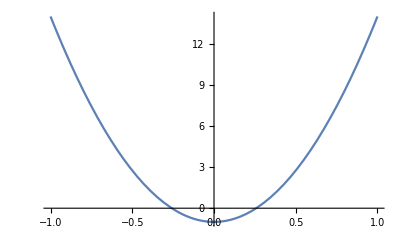

```mathematica
Plot[(-1+15 z^2),{z,-1,1}]
```

```mathematica
15  z^2+3/2  (-1+5 z^2)//Simplify
```

3/2 (-1+15 z^2)

```mathematica
//Simplify
```

{3/2 y (-1+15 z^2),-3/2 x (-1+15 z^2),0}

```mathematica
({{15  z^2+3/2  (-1+5 z^2)}, {-15 x z^2-3/2 x (-1+5 z^2)}, {0}})
```

### higher order as poly * a,b,c

```mathematica
GradYc[m_,l_,x_,y_,z_]:=SGrad[Yc[m,l,x,y,z],{x,y,z}];
GradYs[m_,l_,x_,y_,z_]:=SGrad[Ys[m,l,x,y,z],{x,y,z}];
PertGradYc[m_,l_,x_,y_,z_]:=Curl[SGrad[Yc[m,l,x,y,z],{x,y,z}],{x,y,z}];
PertGradYs[m_,l_,x_,y_,z_]:=Curl[SGrad[Ys[m,l,x,y,z],{x,y,z}],{x,y,z}];
```

#### l = 2

```mathematica
PertGradYc[0,2,x,y,z]-6 z a//Simplify
```

{0,0,0}

```mathematica
PertGradYc[1,2,x,y,z]-4x a-4 z b//Simplify
```

{0,0,0}

```mathematica
PertGradYc[2,2,x,y,z]-4x b+4 y c//Simplify
```

{0,0,0}

```mathematica
PertGradYs[1,2,x,y,z]-4 y a-4 z c//Simplify
```

{0,0,0}

```mathematica
PertGradYs[2,2,x,y,z]-4 x c-4 y b
```

{0,0,0}

#### l = 3

```mathematica
PertGradYc[0,3,x,y,z]-3/2(-1+15 z^2) a//Simplify
```

{0,0,0}

```mathematica
PertGradYc[1,3,x,y,z]-45/2 x z a-3/4(-1+15 z^2)b//Simplify
```

{0,0,0}

```mathematica
PertGradYc[2,3,x,y,z]-3 (-1+6 x^2+9 z^2) a-36 x z b//Simplify
```

{0,0,0}

```mathematica
PertGradYc[3,3,x,y,z]-18 x z a -3 (-1+12 x^2+3 z^2)b//Simplify
```

{0,0,0}

```mathematica
PertGradYs[1,3,x,y,z]+45/2 x y b+3/4(1+30 y^2-15 z^2)c //Simplify
```

{0,0,0}

```mathematica
PertGradYs[2,3,x,y,z]-18 x y a- 18 y z b-18 x  z c /.z^2->1-x^2-y^2//Simplify
```

{0,0,0}

```mathematica
PertGradYs[3,3,x,y,z]+18 y z a- (-1+12 x^2-24 y^2+3 z^2) c//Simplify
```

{0,0,0}

#### rearrange

```mathematica
PertGradYc[0,3,x,y,z]-3/2(-1+15 z^2) a//Simplify
```

{0,0,0}

```mathematica
2/45 PertGradYc[1,3,x,y,z]-1/18 PertGradYc[3,3,x,y,z]- (2/15-2 x^2)b//Simplify
```

{0,0,0}

{0,z,-y}

```mathematica
b
```

{0,z,-y}

```mathematica
c
```

{-z,0,x}

```mathematica
a
```

{y,-x,0}

{-z (1+30 y^2-15 z^2),0,x (1+30 y^2-15 z^2)}

```mathematica
b
```

{0,z,-y}

```mathematica
a.b
```

-x z

```mathematica
a.c
```

```mathematica
a.a
```

x^2+y^2

```mathematica
a.b
```

-x z

```mathematica
a.a
```

x^2+y^2

```mathematica
b
```

{0,z,-y}

```mathematica
x a + y b + z c
```

{x y-z^2,-x^2+y z,-y^2+x z}

{0,3 z (-1+12 x^2+3 z^2),-3 y (-1+12 x^2+3 z^2)}

{0,z,-y}

{x y z,-x^2 z,0}

```mathematica
PertGradYs[1,2,x,y,z]-4 y a-4 z c//Simplify
```

{0,0,0}

```mathematica
PertGradYs[2,2,x,y,z]-4 x c-4 y b
```

{0,0,0}

## Orthogonality

```mathematica
z (-3+14 z^2) a
```

```mathematica
f[z_]:=z; (* low degree poly *)
NIntegrate[f[z]  z (-3+14 z^2)(1-z^2)^(3/2),{z,-1,1}]
```

0.441786

```mathematica
f[z_]:=3/2(-1+15 z^2); (* low degree poly *)
NIntegrate[f[z]  z (-3+14 z^2)(1-z^2)^(3/2),{z,-1,1}]
```

0.

```mathematica
NIntegrate[Yc[3,2,Sqrt[1-z^2]Cos[θ],Sqrt[1-z^2]Sin[θ],z]Yc[2,2,Sqrt[1-z^2]Cos[θ],Sqrt[1-z^2]Sin[θ],z],{z,-1,1},{θ,-π,π}]
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

0.

```mathematica
GradYc[3,2,Sqrt[1-z^2]Cos[θ],Sqrt[1-z^2]Sin[θ],z].PertGradYc[2,2,Sqrt[1-z^2]Cos[θ],Sqrt[1-z^2]Sin[θ],z]//Evaluate
```

```mathematica
f[x_,y_,z_]=PertGradYc[0,1,x,y,z]//Simplify;
g[x_,y_,z_]=PertGradYc[0,3,x,y,z]//Simplify;Integrate[f[Sqrt[1-z^2]Cos[θ],Sqrt[1-z^2]Sin[θ],z].g[Sqrt[1-z^2]Cos[θ],Sqrt[1-z^2]Sin[θ],z],{z,-1,1},{θ,-π,π}]
```

```mathematica
f[x_,y_,z_]=y z;
g[x_,y_,z_]=Yc[0,3,x,y,z]//Simplify;Integrate[f[Sqrt[1-z^2]Cos[θ],Sqrt[1-z^2]Sin[θ],z]g[Sqrt[1-z^2]Cos[θ],Sqrt[1-z^2]Sin[θ],z],{z,-1,1},{θ,-π,π}]
```

0

```mathematica
PertGradYc[0,0,x,y,z]//Simplify
```

{0,0,0}

{y,-x,0}